### Flat universe

```mathematica
a(1+a^4)ϕ''[a]+2(3a^4+2)ϕ'[a]+a(4a^2+k^2)ϕ[a]==0
DSolve[%, ϕ[a], a]
```

a (4 a^2+k^2) ϕ[a]+2 (2+3 a^4) ϕ'[a]+a (1+a^4) ϕ''[a]==0

{{ϕ[a]→(ⅇ^((-1+K[1]^4+k^2 K[1]^6+2 K[1]^8+ⅈ √(k^2 (-4+k^4)) K[1]^3 √(1+K[1]^4))/(K[1] (1+K[1]^4) (1+k^2 K[1]^2+K[1]^4))K[1]1a) C[1])/(a^2 (1+a^4)^(1/4))+(ⅇ^((-1+K[1]^4+k^2 K[1]^6+2 K[1]^8+ⅈ √(k^2 (-4+k^4)) K[1]^3 √(1+K[1]^4))/(K[1] (1+K[1]^4) (1+k^2 K[1]^2+K[1]^4))K[1]1a) C[2] ⅇ^(-2 (-1+K[1]^4+k^2 K[1]^6+2 K[1]^8+ⅈ √(k^2 (-4+k^4)) K[1]^3 √(1+K[1]^4))/(K[1] (1+K[1]^4) (1+k^2 K[1]^2+K[1]^4))K[1]1K[2])K[2]1a)/(a^2 (1+a^4)^(1/4))}}

```mathematica
ϕ[a_]:=(1+a^4)^(1/4)Exp[1/2I ArcTan[a^2]]HeunG[-1,1/4(5-K^2 I),1,5/2,5/2,1/2,a^2I]
```

```mathematica
a(1+a^4)ϕ''[a]+2(3a^4+2)ϕ'[a]+a(4a^2+K^2)ϕ[a]//FullSimplify
```

0

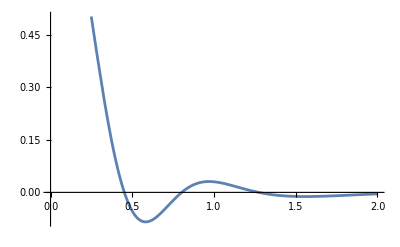

```mathematica
Plot[{ϕ[a]/.{K->10}},{a,0,2}]
```

```mathematica
a(1-a^2)^2y''[a]+2(3a^2-2)(a^2-1)y'[a]+a(4a^2+K^2)y[a]==0
DSolve[%, y[a], a]
```

a (4 a^2+K^2) y[a]+2 (-1+a^2) (-2+3 a^2) y'[a]+a (1-a^2)^2 y''[a]==0

{{y[a]→((1-a)^(1/2 √(-4-K^2)) (1+a)^(-1/2 √(-4-K^2)) (1+a (a+√(-4-K^2))) C[1])/a^3-((1-a)^(-1/2 √(-4-K^2)) (1+a)^(1/2 √(-4-K^2)) (1+a^2+a √(-4-K^2)) (-1+2 a^2-a^4+a^2 K^2+2 a √(-4-K^2)+2 a^3 √(-4-K^2)) C[2])/(2 a^3 √(-4-K^2) (8+K^2) (1+6 a^2+a^4+a^2 K^2))}}

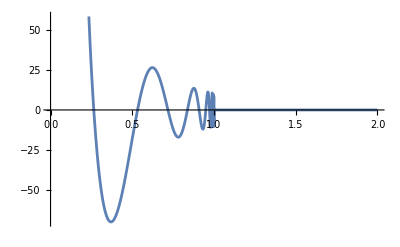

```mathematica
Plot[{Re[((1-a)^(1/2 √(-4-K^2)) (1+a)^(-1/2 √(-4-K^2)) (1+a (a+√(-4-K^2))))/a^3/.{K->10}]
},
{a,0,2}
]
```

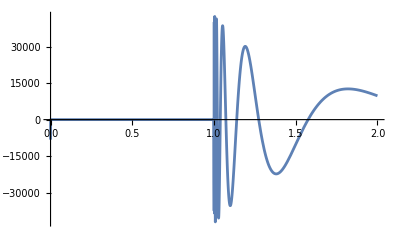

```mathematica
Plot[{Re[((1-a)^(-1/2 √(-4-K^2)) (1+a)^(1/2 √(-4-K^2)) (1+a^2+a √(-4-K^2)) (-1+2 a^2-a^4+a^2 K^2+2 a √(-4-K^2)+2 a^3 √(-4-K^2)))/(2 a^3 √(-4-K^2) (8+K^2) (1+6 a^2+a^4+a^2 K^2))/.{K->10}]
},
{a,0,2}
]
```

```mathematica
Series[((1-a)^(1/2 √(-4-K^2)) (1+a)^(-1/2 √(-4-K^2)) (1+a (a+√(-4-K^2))))/a^3,{a,0,2}]
```

1/a^3+(6+K^2)/(2 a)+1/3 (-8 √(-4-K^2)-K^2 √(-4-K^2))+1/8 (-32-12 K^2-K^4) a+1/30 (8 K^2 √(-4-K^2)+K^4 √(-4-K^2)) a^2+O[a]^3

```mathematica
Series[((1-a)^(-1/2 √(-4-K^2)) (1+a)^(1/2 √(-4-K^2)) (1+a^2+a √(-4-K^2)) (-1+2 a^2-a^4+a^2 K^2+2 a √(-4-K^2)+2 a^3 √(-4-K^2)))/(2 a^3 √(-4-K^2) (8+K^2) (1+6 a^2+a^4+a^2 K^2)),{a,0,2}]
```

-1/(2 (√(-4-K^2) (8+K^2)) a^3)+(-6-K^2)/(4 √(-4-K^2) (8+K^2) a)-1/6+((4+K^2) a)/(16 √(-4-K^2))+(K^2 a^2)/60+O[a]^3

```mathematica
Series[3I(1/(2 Sqrt[4+K^2](8+K^2))((1-a)^(1/2 √(-4-K^2)) (1+a)^(-1/2 √(-4-K^2)) (1+a (a+√(-4-K^2))))/a^3+I((1-a)^(-1/2 √(-4-K^2)) (1+a)^(1/2 √(-4-K^2)) (1+a^2+a √(-4-K^2)) (-1+2 a^2-a^4+a^2 K^2+2 a √(-4-K^2)+2 a^3 √(-4-K^2)))/(2 a^3 √(-4-K^2) (8+K^2) (1+6 a^2+a^4+a^2 K^2))),{a,0,1}]/.{K->1}//FullSimplify
```

1+O[a]^2

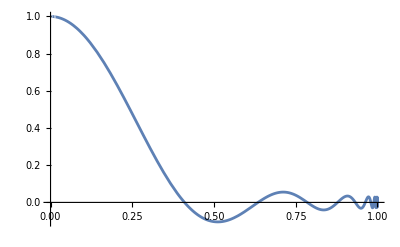

```mathematica
Plot[{3I(1/(2 Sqrt[4+K^2](8+K^2))((1-a)^(1/2 √(-4-K^2)) (1+a)^(-1/2 √(-4-K^2)) (1+a (a+√(-4-K^2))))/a^3+I((1-a)^(-1/2 √(-4-K^2)) (1+a)^(1/2 √(-4-K^2)) (1+a^2+a √(-4-K^2)) (-1+2 a^2-a^4+a^2 K^2+2 a √(-4-K^2)+2 a^3 √(-4-K^2)))/(2 a^3 √(-4-K^2) (8+K^2) (1+6 a^2+a^4+a^2 K^2)))/.{K->10}
},
{a,0,1}
]
```

```mathematica
a(1+a^2)^2y''[a]+2(3a^2+2)(a^2+1)y'[a]+a(4a^2+K^2)y[a]==0
DSolve[%, y[a], a]
```

a (4 a^2+K^2) y[a]+2 (1+a^2) (2+3 a^2) y'[a]+a (1+a^2)^2 y''[a]==0

{{y[a]→(ⅇ^(ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)) C[1])/a^3+(ⅇ^(-ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)) (ⅈ+2 ⅈ a^2+ⅈ a^4-ⅈ a^2 K^2-2 a √(-4+K^2)+2 a^3 √(-4+K^2)) C[2])/(2 a^3 (-8+K^2) √(-4+K^2) (1-6 a^2+a^4+a^2 K^2))}}

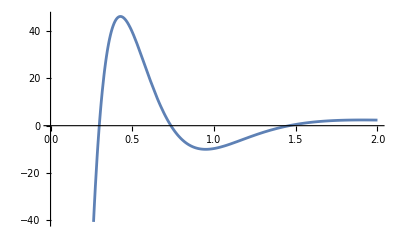

```mathematica
Plot[{Re[(ⅇ^(ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)))/a^3/.{K->10}]
},
{a,0,2}
]
```

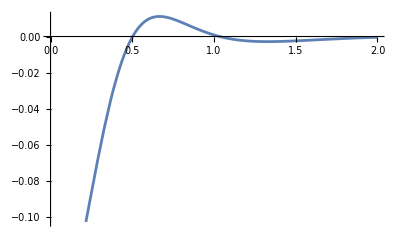

```mathematica
Plot[{Re[(ⅇ^(-ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)) (ⅈ+2 ⅈ a^2+ⅈ a^4-ⅈ a^2 K^2-2 a √(-4+K^2)+2 a^3 √(-4+K^2)))/(2 a^3 (-8+K^2) √(-4+K^2) (1-6 a^2+a^4+a^2 K^2))/.{K->10}]
},
{a,0,2}
]
```

```mathematica
Series[(ⅇ^(ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)))/a^3,{a,0,2}]
```

-1/a^3+(6-K^2)/(2 a)-1/3 ⅈ (-8+K^2) √(-4+K^2)+1/8 (32-12 K^2+K^4) a+1/30 ⅈ √(-4+K^2) (-8 K^2+K^4) a^2+O[a]^3

```mathematica
Series[(ⅇ^(-ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)) (ⅈ+2 ⅈ a^2+ⅈ a^4-ⅈ a^2 K^2-2 a √(-4+K^2)+2 a^3 √(-4+K^2)))/(2 a^3 (-8+K^2) √(-4+K^2) (1-6 a^2+a^4+a^2 K^2)),{a,0,2}]
```

-ⅈ/(2 (-8+K^2) √(-4+K^2) a^3)-(ⅈ (-6+K^2))/(4 (-8+K^2) √(-4+K^2) a)-1/6+1/16 ⅈ √(-4+K^2) a+(K^2 a^2)/60+O[a]^3

```mathematica
Series[3I(1/(2 Sqrt[K^2-4](K^2-8))(ⅇ^(ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)))/a^3+I(ⅇ^(-ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)) (ⅈ+2 ⅈ a^2+ⅈ a^4-ⅈ a^2 K^2-2 a √(-4+K^2)+2 a^3 √(-4+K^2)))/(2 a^3 (-8+K^2) √(-4+K^2) (1-6 a^2+a^4+a^2 K^2))),{a,0,1}]/.{K->10}//FullSimplify
```

1+O[a]^2

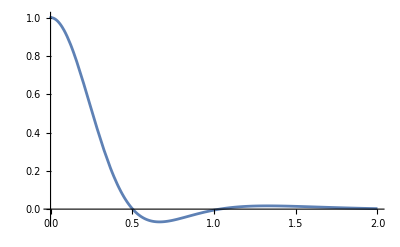

```mathematica
Plot[{3I(1/(2 Sqrt[K^2-4](K^2-8))(ⅇ^(ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)))/a^3+I(ⅇ^(-ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)) (ⅈ+2 ⅈ a^2+ⅈ a^4-ⅈ a^2 K^2-2 a √(-4+K^2)+2 a^3 √(-4+K^2)))/(2 a^3 (-8+K^2) √(-4+K^2) (1-6 a^2+a^4+a^2 K^2)))/.{K->10}
},
{a,0,2},PlotRange-> All
]
```

### Curved universe

Old equation

```mathematica
(*Huen function form*)
Clear[alpha, gamma,ϕ]
alpha[kc_]:=I kc+Sqrt[1-kc^2];
gamma[kc_]:=alpha[kc] (alpha[kc]-1)/2/(alpha[kc]^2+1);
ϕ[kc_,a_]:=Exp[-1/2 (1-I kc) ArcTan[(-I kc+I a^2)/Sqrt[kc^2-1]]/Sqrt[kc^2-1]]Exp[I/4 ArcTan[2 kc I a^2/(a^4+1)]] (1+(2-4kc^2)a^4+a^8)^(1/8) (I a^2/alpha[kc]-1)^(-gamma[kc])(alpha[kc] I a^2+1)^gamma[kc] HeunG[-1/alpha[kc]^2,1/4/alpha[kc](5alpha[kc]-K^2 I),1,5/2,5/2,1/2,a^2I/alpha[kc]];
(a(1+a^4)-2a^3 kc)D[ϕ[kc,a],{a,2}]+(2(3a^4+2)-10a^2 kc)D[ϕ[kc,a],{a,1}]+a(4a^2+K^2)ϕ[kc,a]//FullSimplify
```

0

```mathematica
(*Integration form*)
Clear[f,psi,Phi]
f[kc_,a_]:=3*Sqrt[a^4+(K^2+6*kc)*a^2+1]/Sqrt[K^2+8*kc]/Sqrt[(K^2+6*kc)^2-4]/a^3;  psi[kc_,a_]:=Sqrt[kc-Sqrt[kc^2-1]]*(EllipticPi[-1/2*(kc-Sqrt[kc^2-1])*((K^2+6*kc)-Sqrt[(K^2+6*kc)^2-4]),ArcSin[a/Sqrt[kc-Sqrt[kc^2-1]]],(Sqrt[kc^2-1]-kc)^2]-EllipticPi[-1/2*(kc-Sqrt[kc^2-1])*((K^2+6*kc)+Sqrt[(K^2+6*kc)^2-4]),ArcSin[a/Sqrt[kc-Sqrt[kc^2-1]]],(Sqrt[kc^2-1]-kc)^2]);
 ϕ[kc_,a_]:=f[kc,a]*Sin[Sqrt[K^2+8*kc]*psi[kc,a]];
(a(1+a^4)-2a^3 kc)D[ϕ[kc,a],{a,2}]+(2(3a^4+2)-10a^2 kc)D[ϕ[kc,a],{a,1}]+a(4a^2+K^2)ϕ[kc,a]//FullSimplify
```

0

New equation

```mathematica
(*Huen function form*)
Clear[ϕ]
ϕ[kc_,a_]:=Exp[-1/2 (1-I kc) ArcTan[(-I kc+I a^2)/Sqrt[kc^2-1]]/Sqrt[kc^2-1]]Exp[I/4 ArcTan[2 kc I a^2/(a^4+1)]] (1+(2-4kc^2)a^4+a^8)^(1/8) (I a^2/alpha[kc]-1)^(-gamma[kc])(alpha[kc] I a^2+1)^gamma[kc] HeunG[-1/alpha[kc]^2,1/4/alpha[kc](5alpha[kc]-(K^2-8 kc) I),1,5/2,5/2,1/2,a^2I/alpha[kc]];
(a(1+a^4)-2a^3 kc)D[ϕ[kc,a],{a,2}]+(2(3a^4+2)-10a^2 kc)D[ϕ[kc,a],{a,1}]+a(4a^2+(K^2-8kc))ϕ[kc,a]//FullSimplify
```

0

$Aborted

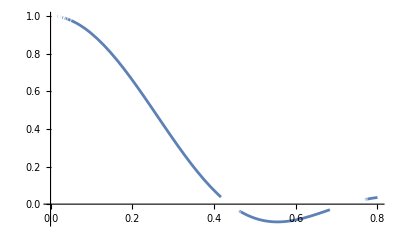

```mathematica
(*Integration form*)
Clear[f,psi,ϕ]
f[kc_,a_]:=3*Sqrt[a^4+(K^2-2*kc)*a^2+1]/K/Sqrt[(K^2-2*kc)^2-4]/a^3;  psi[kc_,a_]:=Sqrt[kc-Sqrt[kc^2-1]]*(EllipticPi[-1/2*(kc-Sqrt[kc^2-1])*((K^2-2*kc)-Sqrt[(K^2-2*kc)^2-4]),ArcSin[a/Sqrt[kc-Sqrt[kc^2-1]]],(Sqrt[kc^2-1]-kc)^2]-EllipticPi[-1/2*(kc-Sqrt[kc^2-1])*((K^2-2*kc)+Sqrt[(K^2-2*kc)^2-4]),ArcSin[a/Sqrt[kc-Sqrt[kc^2-1]]],(Sqrt[kc^2-1]-kc)^2]);
 ϕ[kc_,a_]:=f[kc,a]*Sin[K*psi[kc,a]];
(a(1+a^4)-2a^3 kc)D[ϕ[kc,a],{a,2}]+(2(3a^4+2)-10a^2 kc)D[ϕ[kc,a],{a,1}]+a(4a^2+K^2-8 kc)ϕ[kc,a]//FullSimplify
Plot[ ϕ[0.5,a]/.K->10,{a,0,0.8}]
```

### Add matter

```mathematica
Clear[ode]
r=1;
$Assumptions={m>0,κ>0,k>0};
ode = a(r+m a-2κ a^2+a^4)Phi''[a]+(4r+4 m a-10 κ a^2 +6 a^4)Phi'[a]+a(4 a^2+k^2-8κ)Phi[a]==0;
Phi[a_]:=Sqrt[g[a]]/a^3 Exp[I Integrate[f[b]/Sqrt[1+b^4-2κ b^2 +m b] / g[b], {b,0,a}]];
PhiPrime=D[Phi[a],a];
PhiDoublePrime=D[PhiPrime,a];
newOde=ode/. {Phi[a]->Sqrt[g[a]]/a^3 Exp[I Integrate[f[b]/Sqrt[1+b^4-2κ b^2 +m b] / g[b], {b,0,a}]],Phi'[a]->PhiPrime,Phi''[a]->PhiDoublePrime};
newOde/.{f[a]->a^2,f'[a]->2a}//Simplify
```

(-4 a^4+4 (-2 a^2+k^2-2 κ) g[a]^2+(4 (-1-a m+a^2 κ) g[a] g'[a])/a-(1+a^4+a m-2 a^2 κ) g'[a]^2+(2 g[a] (-ⅈ a^2 m+(1+a^4+a m-2 a^2 κ)^(3/2) g''[a]))/(√(1+a^4+a m-2 a^2 κ)))/(√g[a])==0